# 韧致辐射

带电粒子在加速度下会产生辐射，如果加速度平行于速度方向，则产生的时韧致辐射。

辐射角分布，下面推导时的辐射角分布

加速度；
再考虑粒子再球坐标原点，沿轴方向，简化为观察者在坐标系中的位置表示；
因此可以将辐射角分布化简。

点成用  a . b ，叉乘用Cross[a, b]

首先考虑粒子速度不大（非相对论粒子），即

```mathematica
dPdOmega[n_,β_,βdot_,q_,ε0_,c_]:=Module[{num,den},num=Cross[n,Cross[n-β,βdot]];
den=(1-n.β)^5;
(q^2/(16 π^2 ϵ0 c))*num.num/den]
(*Module[{局部变量},表达式]会创建一组只在 Module 内部有效的局部变量，避免污染外部符号。*)
```

```mathematica
(*定义这三个矢量*)
n={Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]};   (*观察方向*)
β={0,0,β0};    (*非相对论 β0->0*)
βdot={0,0,a0/c}; (*加速度沿 z 轴*)
```

```mathematica
(*加速度与速度平行情况下的辐射角分布*)
dPdOmegaPara[θ_] = Simplify[dPdOmega[n,β,βdot,q,ϵ0,c]]
```

-(a0^2 q^2 Sin[θ]^2)/(16 c^3 π^2 ϵ0 (-1+β0 Cos[θ])^5)

由于β0趋于0，因此辐射角正比于

辐射角分布（极坐标和球坐标）

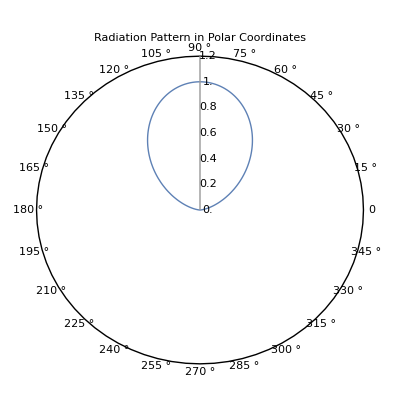

```mathematica
PolarPlot[Sin[θ]^2,{θ,0,π},PolarAxes->True,
PolarTicks->{"Degrees",Automatic},PlotStyle->Thick,PlotLabel->"Radiation Pattern in Polar Coordinates"]
```

```mathematica
SphericalPlot3D[Sin[θ]^2,{θ,0,π},{φ,0,2 π},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"x","y","z"},Boxed->False,Mesh->None]
```

-Graphics3D-

可见在z轴方向上辐射最弱，在垂直于加速度方向上辐射最强

如果速度比较大，比如接近光速，取这个特殊情况

```mathematica
n={Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]};   (*观察方向*)
β={0,0,0.2};    (*相对论 β=0.9*)
βdot={0,0,a0/c}; (*加速度沿 z 轴*)
```

```mathematica
(*加速度与速度平行情况下的辐射角分布*)
dPdOmegaParaRela[θ] = Simplify[dPdOmega[n,β,βdot,q,ϵ0,c]]
```

-(19.7893 a0^2 q^2 Sin[θ]^2)/(c^3 ϵ0 (-5.+1. Cos[θ])^5)

```mathematica
dPdOmegaParaRela[θ] / dPdOmegaPara[θ]
```

(3125. (-1+β0 Cos[θ])^5)/(-5.+1. Cos[θ])^5

```mathematica
assume ={β0 == 0};
f[θ_] = Simplify[dPdOmegaParaRela[θ] / dPdOmegaPara[θ], assume] (*相对论下相比非相对论时的放大因子*)
```

-3125./(-5.+Cos[θ])^5

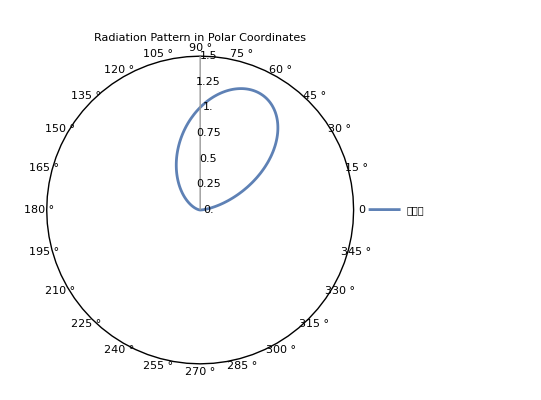

```mathematica
PolarPlot[f[θ]*Sin[θ]^2,{θ,0,π},PolarAxes->True,
PolarTicks->{"Degrees",Automatic},PlotStyle->Thick,PlotLegends->{"相对论"},PlotLabel->"Radiation Pattern in Polar Coordinates"]
```

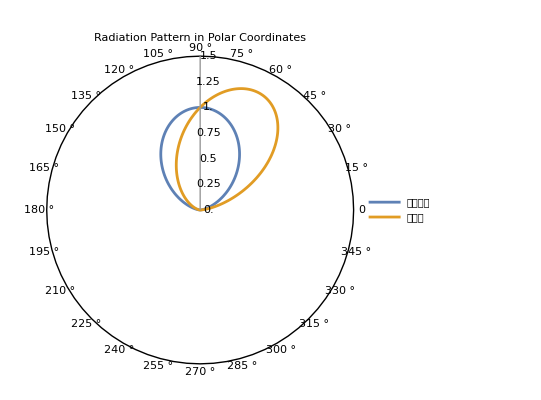

```mathematica
PolarPlot[{Sin[θ]^2,f[θ]*Sin[θ]^2},{θ,0,π},PolarAxes->True,
PolarTicks->{"Degrees",Automatic},PlotStyle->Thick,PlotLegends->{"非相对论","相对论"},PlotLabel->"Radiation Pattern in Polar Coordinates"]
```

```mathematica
SphericalPlot3D[f[θ]*Sin[θ]^2,{θ,0,π},{φ,0,2 π},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"x","y","z"},Boxed->False,Mesh->None]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{Sin[θ]^2, f[θ]*Sin[θ]^2},{θ,0,π},{φ,0,π},Axes->True,AxesOrigin->{0,0,0},PlotLegends->{"非相对论","相对论"},AxesLabel->{"x","y","z"},Boxed->False,Mesh->None]
```

-Graphics3D-

## 随着粒子速度变大，辐射的束流越接近平行于加速度方向，且辐射功率增强。

```mathematica
(*辐射总功率*)
Ptot[β0_]:=Integrate[dPdOmegaPara[θ]*Sin[θ],{θ,0,π},{φ,0,2 π},Assumptions->{0<=β0<1}]

Ptot[β0]
```

ConditionalExpression[-(a0^2 q^2)/(6 c^3 π (-1+β0^2)^3 ϵ0), β0>0]

如果β0接近于0，那么这个辐射总功率变为(拉莫尔公式)